## General generation structure

1. import city data(streets and other entities, osm)
2. use skeleton data of the streets to generate more streets(fake realistic city generation, streets/roads/ways)
3. Classify areas of existing real city using info of existing entities and algorithm https://zero.re/worldsmith/blockassign/)
4. Classify newly generated areas of fake cities: https://zero.re/worldsmith/blockassign/
5. generate entities(e.g. buildings) in the fake generated cities

```mathematica
(*New York City Times Square OSM Import *)
osm=ResourceFunction["OSMImport"][GeoBoundsRegion[{{40.755905,40.769988},{-73.994486,-73.968818}}]]
(*choose tile size and define a grid*)
bounds={{40.755905,40.769988},{-73.994486,-73.968818}};
tileSize=0.001;  (*degrees~111m lat,85m lon near NYC*)
latitudes=Range[bounds[[1,1]],bounds[[1,2]],tileSize];
longitudes=Range[bounds[[2,1]],bounds[[2,2]],tileSize];

tiles=Flatten[Table[GeoBoundingBox[GeoPosition[{lat+tileSize/2,lon+tileSize/2}],Quantity[tileSize*111000/2,"Meters"]],{lat,Most[latitudes]},{lon,Most[longitudes]}],1]
(*Assign OSM features to Tiles*)
```

## New York City Times Square(import and skeleton visualization of Street)

```mathematica
osmNewYork=ResourceFunction["OSMImport"][GeoBoundsRegion[{{40.755905,40.769988},{-73.994486,-73.968818}}]];
```

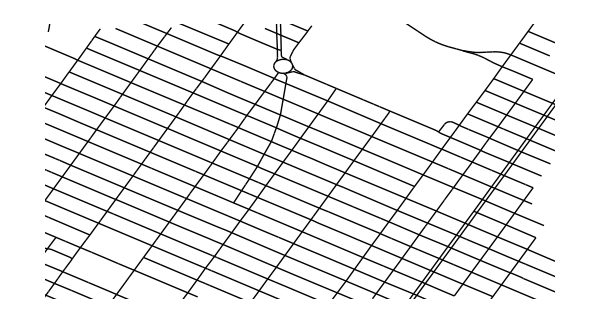

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
GeoGraphics[Values[Line[Values[osmNewYork[["Nodes",#Nodes,"Position"]]]]&/@Select[osmNewYork["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]];

generateLines[openStreetMapData_]:=Values[Line[Values[openStreetMapData[["Nodes",#Nodes,"Position"]]]]&/@Select[openStreetMapData["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]/.
GeoPosition[{a_,b_}]:>{b,a}

Graphics[generateLines[osmNewYork]/. GeoPosition[{lat_,lon_}]:>{lon,lat},PlotRange->{{-73.994,-73.968},{40.756,40.770}},(*your region bounds*)ImageSize->600] (*cropped*)


ImagePartition[Graphics[generateLines[osmNewYork]/. GeoPosition[{lat_,lon_}]:>{lon,lat},PlotRange->{{-73.994,-73.968},{40.756,40.770}},(*your region bounds*)ImageSize->600]
, 75]
```

```mathematica
GeoGraphics[{Values[Line[Values[osmNewYork[["Nodes",#Nodes,"Position"]]]]&/@osmNewYork["Ways"]],GeoMarker[#["Position"]]&/@osmNewYork["Nodes"]}]
```

#### Applying the algorithm to the above data

```mathematica
closedWays=Select[osm["Ways"],Function[w,MatchQ[w["Tags","highway"],"residential"|"primary"|"secondary"|"tertiary"]&&First[w["Nodes"]]===Last[w["Nodes"]]  (*it's a closed ring*)]];

polygons=Polygon[osmNewYork["Nodes",#["Nodes"],"Position"]]&/@closedWays;
```

<||>

### Markov’s Chain

```mathematica
Check discord
```